```mathematica
Images=Import["F:\\Dropbox\\BFcamera Quantum Efficient\\Readout and Dark nosie\\none-47.99-*.tiff","tiff"];
```

```mathematica
data=ImageData[#,"Bit16"]&/@Images;
(*temp=Counts[DeleteCases[Sort@Flatten@#/16,_Rational]]&/@data;*)
temp=Counts[Sort@Flatten@#/16]&/@data;
hist=KeyValueMap[{#1,#2}&,#]&/@temp;
```

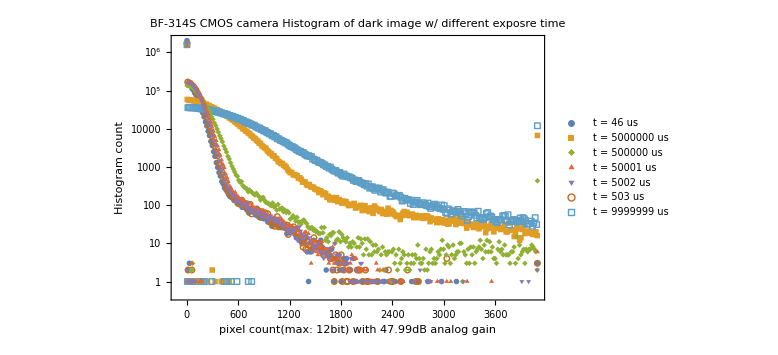

```mathematica
ListLogPlot[hist,AxesOrigin->{-100,Automatic},Frame->True,PlotLegends->{"t = 46 us","t = 5000000 us","t = 500000 us","t = 50001 us","t = 5002 us","t = 503 us","t = 9999999 us"},PlotLabel->"BF-314S CMOS camera Histogram of dark image w/ different exposre time", FrameLabel->{"pixel count(max: 12bit) with 47.99dB analog gain","Histogram count"}, PlotMarkers->{Automatic, Medium}, ImageSize->Large]
```

```mathematica
fldata=(Flatten@#/16)&/@data;
```

```mathematica
sdtemp=StandardDeviation/@fldata;
```

```mathematica
mediantemp=Median/@fldata;
```

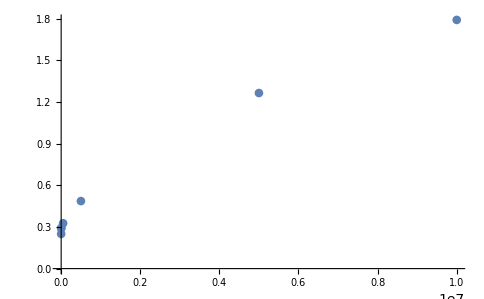

```mathematica
sd=Transpose[{{46,503,5002,50001,500000,5000000,9999999},(Sort@N@sdtemp)/10^(47.99/20)}];
ListPlot@sd
```

```mathematica
Sort@N@sdtemp
```

{62.7266,72.3246,73.8666,82.0081,122.111,317.462,449.65}

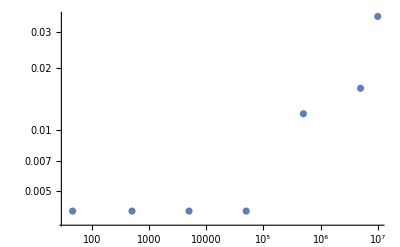

```mathematica
med=Transpose[{{46,503,5002,50001,500000,5000000,9999999},(Sort@N@mediantemp)/10^(47.99/20)}];
ListLogLogPlot@med
```